### Start choosing the example:

```mathematica
t=30;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.010299,Null}

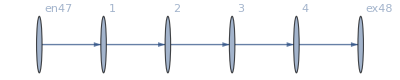

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j49→80.,j50→80.,j51→80.,j52→80.,j53→80.,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80.,jt61→80.,jt62→0.,jt63→80.,jt64→0.,jt65→80.,jt66→0.,u67→255.,u68→175.,u69→95.,u70→15.,u71→255.,u72→175.,u73→95.,u74→15.,u75→15.,u76→255.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.9871×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.9871×10^-17

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→22.7459,u68→20.1639,u69→17.582,u70→15.,u71→22.7459,u72→20.1639,u73→17.582,u74→15.,u75→15.,u76→22.7459|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.00831×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.00831×10^-17

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→24.484,u68→21.3227,u69→18.1613,u70→15.,u71→24.484,u72→21.3227,u73→18.1613,u74→15.,u75→15.,u76→24.484|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.23109×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.23109×10^-16

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→30.0717,u68→25.0478,u69→20.0239,u70→15.,u71→30.0717,u72→25.0478,u73→20.0239,u74→15.,u75→15.,u76→30.0717|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→149.898,u68→104.932,u69→59.966,u70→15.,u71→149.898,u72→104.932,u73→59.966,u74→15.,u75→15.,u76→149.898|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.47684×10^-13

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→255.,u68→175.,u69→95.,u70→15.,u71→255.,u72→175.,u73→95.,u74→15.,u75→15.,u76→255.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.4679×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.4679×10^-16

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→1106.72,u68→742.811,u69→378.906,u70→15.,u71→1106.72,u72→742.811,u73→378.906,u74→15.,u75→15.,u76→1106.72|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→68536.4,u68→45695.9,u69→22855.5,u70→15.,u71→68536.4,u72→45695.9,u73→22855.5,u74→15.,u75→15.,u76→68536.4|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→870144.,u68→580101.,u69→290058.,u70→15.,u71→870144.,u72→580101.,u73→290058.,u74→15.,u75→15.,u76→870144.|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→872843.,u68→581900.,u69→290958.,u70→15.,u71→872843.,u72→581900.,u73→290958.,u74→15.,u75→15.,u76→872843.|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→1.01758×10^6,u68→678389.,u69→339202.,u70→15.,u71→1.01758×10^6,u72→678389.,u73→339202.,u74→15.,u75→15.,u76→1.01758×10^6|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.92515×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.92515×10^-16

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→1.1942×10^6,u68→796137.,u69→398076.,u70→15.,u71→1.1942×10^6,u72→796137.,u73→398076.,u74→15.,u75→15.,u76→1.1942×10^6|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.63778×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.63778×10^-16

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→1.66311×10^6,u68→1.10875×10^6,u69→554381.,u70→15.,u71→1.66311×10^6,u72→1.10875×10^6,u73→554381.,u74→15.,u75→15.,u76→1.66311×10^6|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→4.96168×10^6,u68→3.30779×10^6,u69→1.6539×10^6,u70→15.,u71→4.96168×10^6,u72→3.30779×10^6,u73→1.6539×10^6,u74→15.,u75→15.,u76→4.96168×10^6|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→4.6785×10^7,u68→3.119×10^7,u69→1.5595×10^7,u70→15.,u71→4.6785×10^7,u72→3.119×10^7,u73→1.5595×10^7,u74→15.,u75→15.,u76→4.6785×10^7|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

«7 more identical outputs»

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→7.21578×10^10,u68→4.81052×10^10,u69→2.40526×10^10,u70→15.,u71→7.21578×10^10,u72→4.81052×10^10,u73→2.40526×10^10,u74→15.,u75→15.,u76→7.21578×10^10|>

```mathematica
alpha = 1.89;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.65439×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.65439×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.65439×10^-16

«7 more identical outputs»

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→6.26422×10^17,u68→4.17614×10^17,u69→2.08807×10^17,u70→15.,u71→6.26422×10^17,u72→4.17614×10^17,u73→2.08807×10^17,u74→15.,u75→15.,u76→6.26422×10^17|>

```mathematica
alpha = 1.9;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.16509×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.16509×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.16509×10^-16

«7 more identical outputs»

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→1.68111×10^19,u68→1.12074×10^19,u69→5.6037×10^18,u70→15.,u71→1.68111×10^19,u72→1.12074×10^19,u73→5.6037×10^18,u74→15.,u75→15.,u76→1.68111×10^19|>

```mathematica
alpha = 1.95;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→2.26303×10^33,u68→1.50869×10^33,u69→7.54344×10^32,u70→15.,u71→2.26303×10^33,u72→1.50869×10^33,u73→7.54344×10^32,u74→15.,u75→15.,u76→2.26303×10^33|>

```mathematica
alpha = 1.99;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.55831×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.55831×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.55831×10^-16

«7 more identical outputs»

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→5.97182×10^105,u68→3.98121×10^105,u69→1.99061×10^105,u70→15.,u71→5.97182×10^105,u72→3.98121×10^105,u73→1.99061×10^105,u74→15.,u75→15.,u76→5.97182×10^105|>

```mathematica
alpha = 1.999;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.03522×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.03522×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.03522×10^-16

«7 more identical outputs»

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→5.20079×10^106,u68→3.46719×10^106,u69→1.7336×10^106,u70→15.,u71→5.20079×10^106,u72→3.46719×10^106,u73→1.7336×10^106,u74→15.,u75→15.,u76→5.20079×10^106|>

```mathematica
alpha = 2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.20037×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.20037×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.20037×10^-16

«17 more identical outputs»

<|j49→80,j50→80,j51→80,j52→80,j53→80,j54→0.,j55→0.,j56→0.,j57→0.,j58→0.,jt59→0.,jt60→80,jt61→80,jt62→0.,jt63→80,jt64→0.,jt65→80,jt66→0.,u67→6.61469×10^106,u68→4.4098×10^106,u69→2.2049×10^106,u70→15.,u71→6.61469×10^106,u72→4.4098×10^106,u73→2.2049×10^106,u74→15.,u75→15.,u76→6.61469×10^106|>

### What we this plot for?

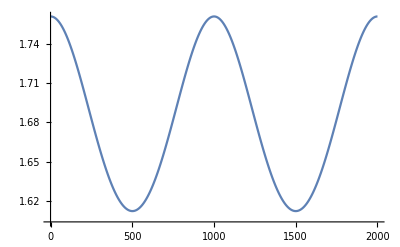

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.